# Q1

-210

6

0

-6

4

-3

-8

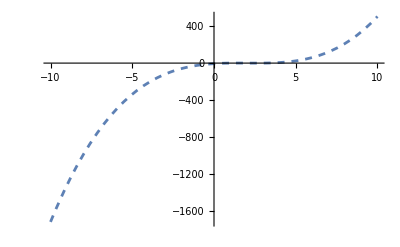

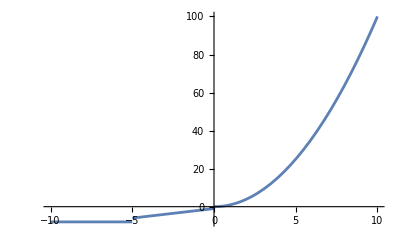

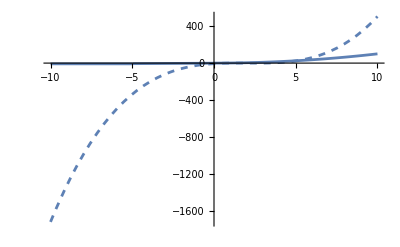

11-12 x+3 x^2

6 (-2+x)

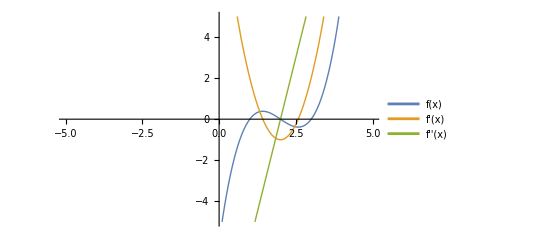

x<1/3 (6-√3)||x>1/3 (6+√3)

1/3 (6-√3)<x<1/3 (6+√3)

x>2

x<2

x==1/3 (6-√3)||x==1/3 (6+√3)

x==2

{-0.3849,{x→2.57735}}

{0.3849,{x→1.42265}}

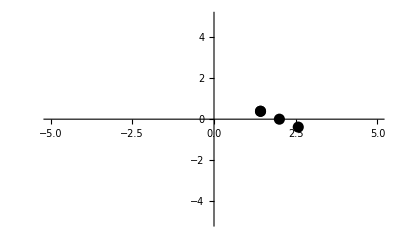

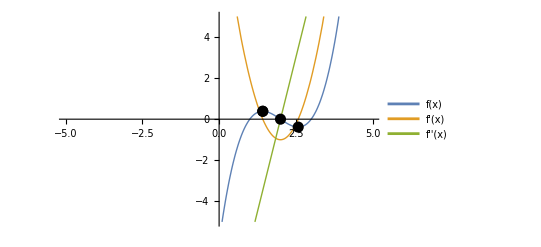

LIMIT EXIST

-3

LIMIT DOES NOT EXIST

LIMIT EXIST

4

```mathematica
(*a*)
f[x_]:=(x-1)(x-2)(x-3)
g[x_]:= Piecewise[{{x^2,x>=0},{x-1,-5<=x<0},{-8,x<-5}}]
(*b*)
f[-4]
f[4]
g[0]
g[-5]
g[2]
g[-2]
g[-8]
(*c*)
p1 = Plot[f[x],{x,-10,10},PlotStyle->Dashed,PlotLegends->"Expressions"]
p2= Plot[g[x],{x,-10,10}]
Show[p1,p2]
(*d*)
h1[x_]=Simplify[D[f[x],{x,1}]]
h2[x_]=Simplify[D[f[x],{x,2}]]
(*e*)
p3 = Plot[{f[x],f'[x],f''[x]},{x,-5,5},PlotStyle->Thick,PlotRange->{{-5,5},{-5,5}},PlotLegends->"Expressions"]
Reduce[f'[x]>0,x](*Increasing*)
Reduce[f'[x]<0,x](*Decreasing*)
Reduce[f''[x]>0,x](*Concave up*)
Reduce[f''[x]<0,x](*Concave Down*)
m1 = Reduce[f'[x]==0,x](*Critical Point*)
m2 = Reduce[f''[x]==0,x](*Inflection Point*)
m3 = FindMinimum[f[x],{x,3}](*Minimum Point*)
m4=FindMaximum[f[x],{x,1}](*Maximum Point*)
(*f*)
p4 = ListPlot[{{m1[[1,2]],f[m1[[1,2]]]},{m2[[2]],f[m2[[2]]]},{m3[[2,1,2]],m3[[1]]},{m4[[2,1,2]],m4[[1]]}},PlotStyle->{Black,PointSize[0.02]},PlotRange->{{-5,5},{-5,5}}]
Show[p3,p4]
(*g*)
LHL = Limit[g[x],x->-2,Direction->-1];
RHL = Limit[g[x],x->-2,Direction->1];
If[LHL == RHL,Print["LIMIT EXIST"];Limit[g[x],x->-2],Print["LIMIT DOES NOT EXIST"]]
LHL = Limit[g[x],x->0,Direction->-1];
RHL = Limit[g[x],x->0,Direction->1];
If[LHL == RHL,Print["LIMIT EXIST"];Limit[g[x],x->0],Print["LIMIT DOES NOT EXIST"]]
LHL = Limit[g[x],x->2,Direction->-1];
RHL = Limit[g[x],x->2,Direction->1];
If[LHL == RHL,Print["LIMIT EXIST"];Limit[g[x],x->2],Print["LIMIT DOES NOT EXIST"]]
```